This file is to generate the figures in Supplementary Section 6

```mathematica
saveDir=NotebookDirectory[]
```

C:\Dropbox\Input_output_theory\Laser_theory\Clean_codes_for_paper\testing\

## Functions and constants

```mathematica
ϕ0 = Quantity["ReducedPlanckConstant"]/(2Quantity["ElementaryCharge"])
```

1/2 ℏ/e

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
res = 1;
Do[
res *= m-j
,{j,0,n-1}];
Return[res]
]
```

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
Return[Factorial[m]/Factorial[m-n]]
]
```

```mathematica
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))]
```

0.388589

```mathematica
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]]
```

0.996133

```mathematica
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.156017

0.987903

```mathematica
Aelem[m_?IntegerQ,rac_?NumericQ,zc_?NumericQ]:=Module[{ϕc,expϕc},
ϕc =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
expϕc=Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
Quiet[ϕc √(m+1) (bigPhi Exp[-ϕc^2/2]Sum[(-1)^n ϕc^(2n)/(1.0 Factorial[n] Factorial[n+1])bracketN[m,n],{n,0,m}]+2 rac)]
]
```

```mathematica
findMinN[zc_?NumericQ]:=Module[{tbAelem,tbAelemDiff,pos},
tbAelem = ParallelTable[ Aelem[j,0.418,zc],{j,0,1000}];
tbAelemDiff=tbAelem[[2;;]]-tbAelem[[;;-2]];

pos=Position[tbAelemDiff,Min[tbAelemDiff]][[1,1]];

Return[{pos+1,tbAelem}]
]
```

```mathematica
{pos1,aList1}=findMinN[150];
```

```mathematica
pos1
```

43

```mathematica
aTrunc =Floor[120];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
```

```mathematica
Aopc=SparseArray[DiagonalMatrix[1/aList1[[pos1]] aList1[[;;aTrunc]],1],{aTrunc+1,aTrunc+1}]; 
AopcD=SparseArray[DiagonalMatrix[1/aList1[[pos1]] aList1[[;;aTrunc]],-1],{aTrunc+1,aTrunc+1}];

AOpc= KroneckerProduct[Aopc,IdentityMatrix[2]];
AOpcD=KroneckerProduct[AopcD,IdentityMatrix[2]];
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
facFunc[n_?IntegerQ]:=Product[AopcDiag[[j]],{j,n}];
```

```mathematica
AopcDiag//Length
```

120

```mathematica
facFunc[2]
```

0.127647

```mathematica
Product[AopcDiag[[j]],{j,Length[n]}]
```

1

```mathematica
coeff = Table[1.00^k/facFunc[k],{k,120}]
```

{3.29588,7.83409,15.5053,27.1004,43.1961,64.077,89.7048,119.732,153.55,190.359,229.25,269.274,309.514,349.132,387.405,423.745,457.704,488.974,517.369,542.815,565.333,585.014,602.006,616.498,628.703,638.851,647.171,653.894,659.239,663.411,666.603,668.987,670.719,671.936,672.755,673.279,673.591,673.76,673.84,673.871,673.881,673.883,673.883,673.874,673.841,673.759,673.594,673.308,672.853,672.175,671.215,669.911,668.195,665.996,663.241,659.858,655.772,650.911,645.205,638.59,631.005,622.397,612.722,601.945,590.041,577.001,562.826,547.534,531.156,513.74,495.349,476.06,455.966,435.173,413.798,391.969,369.822,347.499,325.144,302.905,280.924,259.341,238.288,217.886,198.246,179.466,161.627,144.796,129.023,114.342,100.77,88.3098,76.9481,66.66,57.4088,49.1479,41.823,35.3737,29.7354,24.8411,20.6228,17.0129,13.946,11.3588,9.19217,7.39068,5.90361,4.68495,3.69345,2.89261,2.25044,1.73922,1.3352,1.01821,0.771293,0.58035,0.433757,0.322023,0.237471,0.173947}

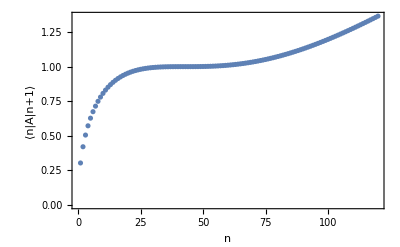

```mathematica
ListPlot[AopcDiag,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","⟨n|A|n+1⟩"}]
```

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
AOP=SparseArray[DiagonalMatrix[√(1.0 Range[400]),1]];
AOP[[;;10,;;10]]//MatrixForm
```

(0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.41421 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.73205 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2.23607 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.44949 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.64575 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.82843 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

### Laser system functions

```mathematica
combineOps[op1_,op2_]:=Module[{top},
top = TensorProduct[op1,op2];
top = Flatten[Transpose[top,{1,3,4,2}],1];
top = Flatten[Transpose[top,{3,1,2}],1];
Return[topᵀ]
]
```

```mathematica
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( combineOps[hac,iOp]-combineOps[iOp,hac]);
pumpSO = -1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
normalLossSO = -1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
lossSO = -1/2(combineOps[AOpcᵀ.AOpc,iOp]+combineOps[iOp,AOpcᵀ.AOpc]-2 combineOps[AOpc,AOpcᵀ]);
```

```mathematica
iOp=SparseArray[IdentityMatrix[Length[aOp]]];
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
tempFun2[lambda_?NumericQ,gr_?NumericQ]:=Module[{γ,g},

γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{nAvg,rate}]
]
```

```mathematica
coh[α_,nMax_?IntegerQ]:=Module[{},
Table[Exp[-Abs[α]^2/2] (1.0 α^j)/(√Factorial[j]),{j,0,nMax}]
]
```

```mathematica
coh2[α_,nMax_?IntegerQ]:=Module[{},
Table[Exp[-Abs[α]^2/2] (1.0 α^j)/factorial[[j+1]],{j,0,nMax}]
]
```

```mathematica
factorial=Table[√(1.0Factorial[j]),{j,0,500}];
```

### Wigner distribution related functions

```mathematica
generateVectCh[state_,chMeshx_,chMeshy_]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];
dx=chMeshx[[2]]-chMeshx[[1]];
dy=chMeshy[[2]]-chMeshy[[1]];
character = ParallelTable[
{x0,y0}=chMesh2d[[j]];
chMtx = MatrixExp[ⅈ(x0+ⅈ y0) AOP†+ⅈ (x0-ⅈ y0) AOP];
Tr[KroneckerProduct[state,state*].chMtx[[;;Length[state],;;Length[state]]]]
,{j,Length[chMesh2d]}];

Return[{chMesh2d,character}]
]
```

```mathematica
checkChMesh[chMeshx_,chMeshy_,dataDir_?DirectoryQ]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD,fns,name4Compare,fnMatch,notExistCoord,fnsGB},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];

fns=FileNames["*",dataDir];
fns = StringSplit[#,"\\"][[-1]]&/@fns;
fnsGB=GroupBy[fns,Round[1.0 ToExpression[StringSplit[#,"_"][[;;2]]],0.1]&];

notExistCoord= {};
Do[
{x0,y0}=chMesh2d[[j]];
fnMatch=fnsGB[Round[1.0 {x0,y0},0.1]];
If[MissingQ[fnMatch],
(*Print[j];*)
AppendTo[notExistCoord,{x0,y0}];
]
,{j,Length[chMesh2d]}];
Return[notExistCoord]
]
```

```mathematica
checkChMesh2[chMeshx_,chMeshy_,dataDir_?DirectoryQ]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD,fns,name4Compare,fnMatch,notExistCoord,fnsGB,fn},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];

notExistCoord= {};
Do[
{x0,y0}=chMesh2d[[j]];
fn = FileNameJoin[{dataDir,ToString[Chop[x0]]<>"_"<>ToString[Chop[y0]]<>"_AOP.mat"}];
If[FileExistsQ[fn],
,
(*Print[j];*)
AppendTo[notExistCoord,{x0,y0}];
]
,{j,Length[chMesh2d]}];
Return[notExistCoord]
]
```

```mathematica
generateMissingPts[missing_,dataDir_?DirectoryQ]:=Module[{temp,x0,y0,chMtx,fn},
temp = ParallelTable[
{x0,y0}=missing[[j]];
chMtx = MatrixExp[ⅈ(x0+ⅈ y0) AOP†+ⅈ (x0-ⅈ y0) AOP];
fn = FileNameJoin[{dataDir,ToString[Chop[x0]]<>"_"<>ToString[Chop[y0]]<>"_AOP.mat"}];
Export[fn,Chop[chMtx]];
,{j,Length[missing]}];
]
```

```mathematica
Clear[generateVectCh1PROBLEM]
```

```mathematica
generateVectCh1PROBLEM[state_,chMeshx_,chMeshy_,dataDir_?DirectoryQ]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD,fns,name4Compare,fnMatch},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];

fns=FileNames["*",dataDir];
fns = StringSplit[#,"\\"][[-1]]&/@fns;


dx=chMeshx[[2]]-chMeshx[[1]];
dy=chMeshy[[2]]-chMeshy[[1]];
character = ParallelTable[
{x0,y0}=chMesh2d[[j]];
name4Compare = ToString[Chop[x0]]<>"_"<>ToString[Chop[y0]];
fnMatch = Select[fns,StringStartsQ[#,name4Compare]&];
If[Length[fnMatch]≠0,
chMtx=Import[FileNameJoin[{dataDir,fnMatch[[1]]}]][[1]];
,
Print["Warning: {x,y} = "<>ToString[{x0,y0}]<>" does not found. Recalculating the Displacement operator."];
chMtx = MatrixExp[ⅈ(x0+ⅈ y0) AOP†+ⅈ (x0-ⅈ y0) AOP]

];

Tr[KroneckerProduct[state,state*].chMtx[[;;Length[state],;;Length[state]]]]
,{j,Length[chMesh2d]}];

Return[{chMesh2d,character}]
]
```

```mathematica
generateVectCh2PROBLEM[state_,chMeshx_,chMeshy_,dataDir_?DirectoryQ]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD,fns,name4Compare,fnMatch,fnsGB},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];

fns=FileNames["*",dataDir];
fns = StringSplit[#,"\\"][[-1]]&/@fns;
fnsGB=GroupBy[fns,N[ToExpression[StringSplit[#,"_"][[;;2]]]]&];

dx=chMeshx[[2]]-chMeshx[[1]];
dy=chMeshy[[2]]-chMeshy[[1]];
character = ParallelTable[
{x0,y0}=chMesh2d[[j]];
fnMatch=fnsGB[[Key[{x0,y0}]]];
If[MissingQ[fnMatch],
chMtx = MatrixExp[ⅈ(x0+ⅈ y0) AOP†+ⅈ (x0-ⅈ y0) AOP];
Export[FileNameJoin[{dataDir,ToString[Chop[x0]]<>"_"<>ToString[Chop[y0]]<>"_AOP.mat"}],Chop[chMtx]];
AssociateTo[fnsGB,{dx,dy}->{ToString[Chop[x0]]<>"_"<>ToString[Chop[y0]]<>"_AOP.mat"}]
,
chMtx=Import[FileNameJoin[{dataDir,fnMatch[[1]]}]][[1]];
];

Tr[KroneckerProduct[state,state*].chMtx[[;;Length[state],;;Length[state]]]]
,{j,Length[chMesh2d]}];

Return[{chMesh2d,character}]
]
```

```mathematica
generateVectCh3[state_,chMeshx_,chMeshy_,dataDir_?DirectoryQ]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD,fns,name4Compare,fnMatch,fnsGB},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];

fns=FileNames["*",dataDir];
fns = StringSplit[#,"\\"][[-1]]&/@fns;
fnsGB=GroupBy[fns,N[ToExpression[StringSplit[#,"_"][[;;2]]]]&];

dx=chMeshx[[2]]-chMeshx[[1]];
dy=chMeshy[[2]]-chMeshy[[1]];
character = ParallelTable[
{x0,y0}=chMesh2d[[j]];
fnMatch=fnsGB[[Key[N[{x0,y0}]]]];
If[MissingQ[fnMatch],
Print["Warning: {x,y} = "<>ToString[{x0,y0}]<>" does not found. Return 0 matrix for this point."];
chMtx=SparseArray[{},Dimensions[AOP]]
,
chMtx=Import[FileNameJoin[{dataDir,fnMatch[[1]]}]][[1]];
];

Tr[KroneckerProduct[state,state*].chMtx[[;;Length[state],;;Length[state]]]]
,{j,Length[chMesh2d]}];

Return[{chMesh2d,character}]
]
```

```mathematica
generateVectCh4[state_,chMeshx_,chMeshy_,dataDir_?DirectoryQ]:=Module[{temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD,fns,name4Compare,fnMatch,fnsGB,fn},

chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];

dx=chMeshx[[2]]-chMeshx[[1]];
dy=chMeshy[[2]]-chMeshy[[1]];
character = ParallelTable[
{x0,y0}=chMesh2d[[j]];
fn = FileNameJoin[{dataDir,ToString[Chop[x0]]<>"_"<>ToString[Chop[y0]]<>"_AOP.mat"}];
If[FileExistsQ[fn],
chMtx=Import[fn][[1]];
,
Print["Warning: {x,y} = "<>ToString[{x0,y0}]<>" does not found. Return 0 matrix for this point."];
chMtx=SparseArray[{},Dimensions[AOP]]
];

Tr[KroneckerProduct[state,state*].chMtx[[;;Length[state],;;Length[state]]]]
,{j,Length[chMesh2d]}];

Return[{chMesh2d,character}]
]
```

```mathematica
solveWD[character_,chMesh_,wigMesh_]:=Module[{wignerD,x0,y0,xL,yL,dx,dy},
xL=Sort[Union[chMesh[[All,1]]]];
yL=Sort[Union[chMesh[[All,2]]]];
dx = xL[[2]]-xL[[1]];
dy=yL[[2]]-yL[[1]];
wignerD=ParallelTable[
{x0,y0}=wigMesh[[j]];
{x0,y0,dx dy 1/π^2(Exp[-2ⅈ x0 chMesh[[All,1]]-2ⅈ y0 chMesh[[All,2]]]).character}
,{j,Length[wigMesh]}];
Return[wignerD]
]
```

```mathematica
generateVectWD[state_,chMeshx_,chMeshy_,WigMesh_]:=Module[{(*temp,chMesh2d,character,x0,y0,chMtx,dx,dy,wignerD*)},
chMesh2d=Transpose[{Flatten[ConstantArray[chMeshx,Length[chMeshy]]],Flatten[Transpose[ConstantArray[chMeshy,Length[chMeshx]]]]}];
dx=chMeshx[[2]]-chMeshx[[1]];
dy=chMeshy[[2]]-chMeshy[[1]];
character = ParallelTable[
{x0,y0}=chMesh2d[[j]];
chMtx = MatrixExp[ⅈ(x0+ⅈ y0) AOP†+ⅈ (x0-ⅈ y0) AOP];
Tr[KroneckerProduct[state,state*].chMtx[[;;Length[state],;;Length[state]]]]
,{j,Length[chMesh2d]}];

wignerD=ParallelTable[
{x0,y0}=WigMesh[[j]];
{x0,y0,dx dy 1/π^2(Exp[-2ⅈ x0 chMesh2d[[All,1]]-2ⅈ y0 chMesh2d[[All,2]]]).character}
,{j,Length[WigMesh]}];
Return[wignerD]
]
```

## Flatten-top state for the ABOCC operator Z_c=150

```mathematica
lambdaA = 3.58; gc = lambdaA/2 √(1.0/(lambdaA-2.))
```

1.42405

```mathematica
tempfun[lambdaA,1.03]
```

-10.8895

```mathematica
1.01gc
```

1.43829

```mathematica
superOp = 1.0 lossSO + lambdaA pumpSO + 1.0gc HacSO;
```

```mathematica
{eigValR1,eigVectR1}=Eigensystem[superOp,-20];
```

```mathematica
steady = Partition[Chop[eigVectR1[[-1]]],Length[aOp]];
steady = steady/Tr[steady];
```

```mathematica
stateCav= sBasis[[1]].steady.sBasis[[1]]†+sBasis[[2]].steady.sBasis[[2]]†;
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤120,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav]]^2];
Return[diff^(1/2)]]
```

```mathematica
FindMinimum[testFun[x],{x,0.99,1.01}]
```

{0.00384215,{x→1.00059}}

```mathematica
coeff={1};
For[k=1,k≤120,k+=1,
AppendTo[coeff,1.0005925508517828/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna = coeff/normFac;
```

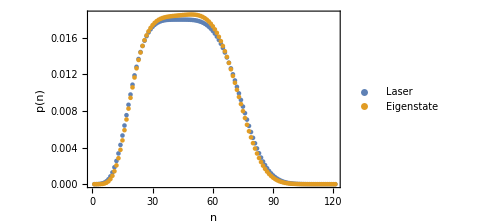

```mathematica
ListPlot[{Chop[Diagonal[stateCav]],stateAna^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

```mathematica
mesh2=Table[
{x,y}
,{x,0,12,0.05}
,{y,-5,5,0.05}]; 
mesh2 = Flatten[mesh2,1];
```

```mathematica
basis2 = ParallelTable[
{x0,y0}=mesh2[[k]];
If[x0==0&&y0==0,
Normal[SparseArray[{1}->1,Length[aop]]]
,coh2[x0+ⅈ y0,Length[aop]-1]
]
,{k,Length[mesh2]}];
Speak["This is done"]
```

```mathematica
qFuncState=Flatten[#]&/@Transpose[{mesh2,Abs[basis2*.stateAna]^2}];
qFuncState//Dimensions
```

{48441,3}

```mathematica
ListDensityPlot[Chop[qFuncState],ColorFunction->"TemperatureMap",PlotRange->Full]
```

-Graphics-

### Most narrowest laser state and the corresponding eigenstate of ABOCC

```mathematica
narrowSol = FindMinimum[tempfun[lambdaA,gr],{gr,1.0,0.9,1.1},AccuracyGoal->3,PrecisionGoal->3]
```

{-10.8897,{gr→1.03052}}

```mathematica
tempfun[lambdaA,gr/.narrowSol[[2]]]
```

-10.8897

```mathematica
gr gc/.narrowSol[[2]]
```

1.46752

```mathematica
superOp = 1.0 lossSO + lambdaA pumpSO + (gr/.narrowSol[[2]])gc HacSO;
```

```mathematica
{eigValR2,eigVectR2}=Eigensystem[superOp,-20];
```

```mathematica
steady2 = Partition[Chop[eigVectR2[[-1]]],Length[aOp]];
steady2 = steady2/Tr[steady2];
```

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤120,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1.02,0.99,1.04},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00486432,{alpha→1.02251}}

```mathematica
coeff={1};
For[k=1,k≤120,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna2 = coeff/normFac;
```

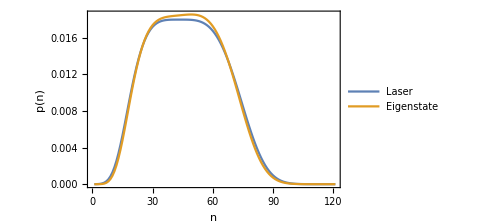

```mathematica
ListPlot[{Chop[Diagonal[stateCav]],stateAna^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

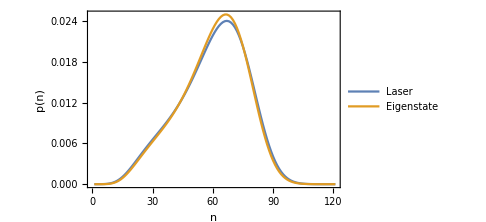

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],stateAna2^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

```mathematica
qFuncState2=Flatten[#]&/@Transpose[{mesh2,Abs[basis2*.stateAna2]^2}];
qFuncState2//Dimensions
```

{48441,3}

### Solve the Wigner function

#### Flat-top state

```mathematica
dataDir=FileNameJoin[{saveDir,"data_files"}];
If[Not[DirectoryQ[dataDir]],CreateDirectory[dataDir]]
```

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

{0.342008,Null}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

0

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser, chFun2Dlaser}=generateVectCh4[stateAna,chMeshx,chMeshy,dataDir];
]
]
```

{46.1226,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,0,12,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{12221,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{3.63427,Null}

```mathematica
Speak["This is done"]
```

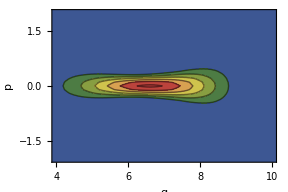

```mathematica
ListContourPlot[wignerD
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/6
,PlotRange->{{4,10},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

#### Narrow linewidth state

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

0

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser2, chFun2Dlaser2}=generateVectCh4[stateAna2,chMeshx,chMeshy,dataDir];
]
]
```

{36.6937,Null}

```mathematica
chFun2DlaserAll2=SparseArray[Join[chFun2Dlaser2,chFun2DlaserEx]];
chMesh2DlaserAll2=Join[chMesh2Dlaser2,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD2 = solveWD[chFun2DlaserAll2,chMesh2DlaserAll2,wigMesh];
]
```

{3.36205,Null}

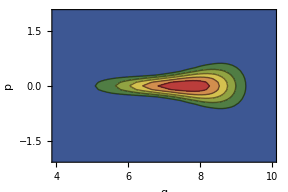

```mathematica
ListContourPlot[wignerD2
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/6
,PlotRange->{{4,10},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

#### Coh state

```mathematica
cohState1 = coh2[√Abs[stateAna*.aop†.aop.stateAna],Length[aop]-1];
cohState1//Dimensions
```

{121}

```mathematica
Abs[stateAna*.aop†.aop.stateAna]
```

45.8777

```mathematica
cohState2 = coh2[√Abs[stateAna2*.aop†.aop.stateAna2],Length[aop]-1];
cohState2//Dimensions
```

{121}

```mathematica
Abs[stateAna2*.aop†.aop.stateAna2]
```

58.8257

```mathematica
chMeshxc=Range[-3.,3.,0.1];
chMeshyc=Range[-3.,3.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshxc,chMeshyc,dataDir];
]
```

{0.237304,Null}

```mathematica
notExist = checkChMesh2[chMeshxc,chMeshyc,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshxc,chMeshyc,dataDir];
]
```

0

```mathematica
AbsoluteTiming[
{chMesh2coh1, chFun2Dcoh1}=generateVectCh4[cohState1,chMeshxc,chMeshyc,dataDir];
]
```

{99.1843,Null}

```mathematica
chMeshxExc=Join[Range[-10.,-3.1,0.1],Range[3.1,10,0.1]];
chMeshyExc=Join[Range[-10.,-3.1,0.1],Range[3.1,10,0.1]];
```

```mathematica
chMeshExMeshc=Transpose[{Flatten[ConstantArray[chMeshxExc,Length[chMeshyExc]]],Flatten[Transpose[ConstantArray[chMeshyExc,Length[chMeshxExc]]]]}];
```

```mathematica
chFun2DCohEx=ConstantArray[0,Length[chMeshExMeshc]];
```

```mathematica
chFun2DCohAll=SparseArray[Join[chFun2Dcoh1,chFun2DCohEx]];
chMesh2DCohAll=Join[chMesh2coh1,chMeshExMeshc];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,0,12,0.1},{y,-6,6,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{14641,2}

```mathematica
AbsoluteTiming[
wignerDcoh1 = solveWD[chFun2DCohAll,chMesh2DCohAll,wigMesh];
]
```

{4.61309,Null}

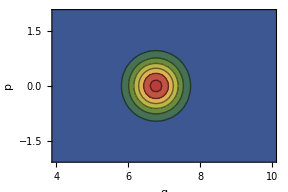

```mathematica
ListContourPlot[wignerDcoh1
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/6
(*,AspectRatio->1*)
,PlotRange->{{4,10},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

```mathematica
AbsoluteTiming[
{chMesh2coh2, chFun2Dcoh2}=generateVectCh4[cohState2,chMeshxc,chMeshyc,dataDir];
]
```

{28.8149,Null}

```mathematica
chFun2DCohAll2=SparseArray[Join[chFun2Dcoh2,chFun2DCohEx]];
chMesh2DCohAll2=Join[chMesh2coh2,chMeshExMeshc];
```

```mathematica
AbsoluteTiming[
wignerDcoh2 = solveWD[chFun2DCohAll2,chMesh2DCohAll2,wigMesh];
]
```

{4.51546,Null}

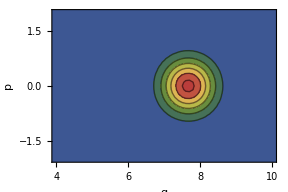

```mathematica
ListContourPlot[wignerDcoh2
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/6
(*,AspectRatio->1*)
,PlotRange->{{4,10},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Numerical solution

```mathematica
sop=1/(2 ⅈ)(eop-eop†);
cop=1/2(eop+eop†);
```

```mathematica
(stateAna*.cop.stateAna)
```

0.999389

```mathematica
Print["Δx^2 = ", stateAna*.reOp.reOp.stateAna-(stateAna*.reOp.stateAna)^2]
Print["Δp^2 = ",stateAna*.imOp.imOp.stateAna-(stateAna*.imOp.stateAna)^2]
Print["Δx Δp = ",√(stateAna*.reOp.reOp.stateAna-(stateAna*.reOp.stateAna)^2)√(stateAna*.imOp.imOp.stateAna-(stateAna*.imOp.stateAna)^2)]
Print["⟨n⟩ = ",stateAna*.aop†.aop.stateAna]
Print["Δn^2 = ",stateAna*.aop†.aop.aop†.aop.stateAna-(stateAna*.aop†.aop.stateAna)^2]
Print["ΔS = ",√(stateAna*.sop.sop.stateAna-(stateAna*.sop.stateAna)^2)]
Print["ΔS^2 = ",stateAna*.sop.sop.stateAna-(stateAna*.sop.stateAna)^2]
Print["ΔS Δn = ",√(stateAna*.aop†.aop.aop†.aop.stateAna-(stateAna*.aop†.aop.stateAna)^2)√(stateAna*.sop.sop.stateAna-(stateAna*.sop.stateAna)^2)]
Print["ΔS^2 Δn^2 / ⟨c⟩^2 = ",(stateAna*.aop†.aop.aop†.aop.stateAna-(stateAna*.aop†.aop.stateAna)^2)(stateAna*.sop.sop.stateAna-(stateAna*.sop.stateAna)^2)/((stateAna*.cop.stateAna)^2)]
```

Δx^2 = 1.77984

Δp^2 = 0.0477235+0. ⅈ

Δx Δp = 0.291445+0. ⅈ

⟨n⟩ = 45.8777

Δn^2 = 305.674

ΔS = 0.0349085+0. ⅈ

ΔS^2 = 0.0012186+0. ⅈ

ΔS Δn = 0.610324+0. ⅈ

ΔS^2 Δn^2 / ⟨c⟩^2 = 0.37295+0. ⅈ

```mathematica
Print["Δx^2 = ", stateAna2*.reOp.reOp.stateAna2-(stateAna2*.reOp.stateAna2)^2]
Print["Δp^2 = ",stateAna2*.imOp.imOp.stateAna2-(stateAna2*.imOp.stateAna2)^2]
Print["Δx Δp = ",√(stateAna2*.reOp.reOp.stateAna2-(stateAna2*.reOp.stateAna2)^2)√(stateAna2*.imOp.imOp.stateAna2-(stateAna2*.imOp.stateAna2)^2)]
Print["⟨n⟩ = ",stateAna2*.aop†.aop.stateAna2]
Print["Δn^2 = ",stateAna2*.aop†.aop.aop†.aop.stateAna2-(stateAna2*.aop†.aop.stateAna2)^2]
Print["ΔS = ",√(stateAna2*.sop.sop.stateAna2-(stateAna2*.sop.stateAna2)^2)]
Print["ΔS^2 = ",stateAna2*.sop.sop.stateAna2-(stateAna2*.sop.stateAna2)^2]
Print["ΔS Δn = ",√(stateAna2*.aop†.aop.aop†.aop.stateAna2-(stateAna2*.aop†.aop.stateAna2)^2)√(stateAna2*.sop.sop.stateAna2-(stateAna2*.sop.stateAna2)^2)]
Print["ΔS^2 Δn^2 / ⟨c⟩^2 = ",(stateAna2*.aop†.aop.aop†.aop.stateAna2-(stateAna2*.aop†.aop.stateAna2)^2)(stateAna2*.sop.sop.stateAna2-(stateAna2*.sop.stateAna2)^2)/((stateAna2*.cop.stateAna2)^2)]
```

Δx^2 = 1.31312

Δp^2 = 0.0755432+0. ⅈ

Δx Δp = 0.314956+0. ⅈ

⟨n⟩ = 58.8257

Δn^2 = 273.313

ΔS = 0.0340124+0. ⅈ

ΔS^2 = 0.00115685+0. ⅈ

ΔS Δn = 0.562299+0. ⅈ

ΔS^2 Δn^2 / ⟨c⟩^2 = 0.316547+0. ⅈ

```mathematica
Print["Δx^2 = ", cohState1*.reOp.reOp.cohState1-(cohState1*.reOp.cohState1)^2]
Print["Δp^2 = ",cohState1*.imOp.imOp.cohState1-(cohState1*.imOp.cohState1)^2]
Print["Δx Δp = ",√(cohState1*.reOp.reOp.cohState1-(cohState1*.reOp.cohState1)^2)√(cohState1*.imOp.imOp.cohState1-(cohState1*.imOp.cohState1)^2)]
Print["⟨n⟩ = ",cohState1*.aop†.aop.cohState1]
Print["Δn^2 = ",cohState1*.aop†.aop.aop†.aop.cohState1-(cohState1*.aop†.aop.cohState1)^2]
Print["ΔS = ",√(cohState1*.sop.sop.cohState1-(cohState1*.sop.cohState1)^2)]
Print["ΔS^2 = ",cohState1*.sop.sop.cohState1-(cohState1*.sop.cohState1)^2]
Print["ΔS Δn = ",√(cohState1*.aop†.aop.aop†.aop.cohState1-(cohState1*.aop†.aop.cohState1)^2)√(cohState1*.sop.sop.cohState1-(cohState1*.sop.cohState1)^2)]
Print["ΔS^2 Δn^2 / ⟨c⟩^2 = ",(cohState1*.aop†.aop.aop†.aop.cohState1-(cohState1*.aop†.aop.cohState1)^2)(cohState1*.sop.sop.cohState1-(cohState1*.sop.cohState1)^2)/((cohState1*.cop.cohState1)^2)]
```

Δx^2 = 0.25

Δp^2 = 0.25+0. ⅈ

Δx Δp = 0.25+0. ⅈ

⟨n⟩ = 45.8777

Δn^2 = 45.8777

ΔS = 0.074027+0. ⅈ

ΔS^2 = 0.00547999+0. ⅈ

ΔS Δn = 0.501408+0. ⅈ

ΔS^2 Δn^2 / ⟨c⟩^2 = 0.252799+0. ⅈ

```mathematica
Print["Δx^2 = ", cohState2*.reOp.reOp.cohState2-(cohState2*.reOp.cohState2)^2]
Print["Δp^2 = ",cohState2*.imOp.imOp.cohState2-(cohState2*.imOp.cohState2)^2]
Print["Δx Δp = ",√(cohState2*.reOp.reOp.cohState2-(cohState2*.reOp.cohState2)^2)√(cohState2*.imOp.imOp.cohState2-(cohState2*.imOp.cohState2)^2)]
Print["⟨n⟩ = ",cohState2*.aop†.aop.cohState2]
Print["Δn^2 = ",cohState2*.aop†.aop.aop†.aop.cohState2-(cohState2*.aop†.aop.cohState2)^2]
Print["ΔS = ",√(cohState2*.sop.sop.cohState2-(cohState2*.sop.cohState2)^2)]
Print["ΔS^2 = ",cohState2*.sop.sop.cohState2-(cohState2*.sop.cohState2)^2]
Print["ΔS Δn = ",√(cohState2*.aop†.aop.aop†.aop.cohState2-(cohState2*.aop†.aop.cohState2)^2)√(cohState2*.sop.sop.cohState2-(cohState2*.sop.cohState2)^2)]
Print["ΔS^2 Δn^2 / ⟨c⟩^2 = ",(cohState2*.aop†.aop.aop†.aop.cohState2-(cohState2*.aop†.aop.cohState2)^2)(cohState2*.sop.sop.cohState2-(cohState2*.sop.cohState2)^2)/((cohState2*.cop.cohState2)^2)]
```

Δx^2 = 0.25

Δp^2 = 0.25+0. ⅈ

Δx Δp = 0.25+0. ⅈ

⟨n⟩ = 58.8257

Δn^2 = 58.8257

ΔS = 0.0653329+0. ⅈ

ΔS^2 = 0.00426838+0. ⅈ

ΔS Δn = 0.50109+0. ⅈ

ΔS^2 Δn^2 / ⟨c⟩^2 = 0.252169+0. ⅈ

### Calculate the p noise as we increase the eigenvalues

```mathematica
{pos1,aList1}=findMinN[150];
```

```mathematica
pos1
```

43

```mathematica
aTrunc =Floor[120];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
```

```mathematica
Aopc=SparseArray[DiagonalMatrix[(1/aList1[[pos1]])aList1[[;;aTrunc]],1],{aTrunc+1,aTrunc+1}]; 
AopcD=SparseArray[DiagonalMatrix[(1/aList1[[pos1]])aList1[[;;aTrunc]],-1],{aTrunc+1,aTrunc+1}];

AOpc= KroneckerProduct[Aopc,IdentityMatrix[2]];
AOpcD=KroneckerProduct[AopcD,IdentityMatrix[2]];
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
facFunc[n_?IntegerQ]:=Product[AopcDiag[[j]],{j,n}];
```

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
sop=1/(2 ⅈ)(eop-eop†);
cop=1/2(eop+eop†);
```

```mathematica
coeff={1};
For[k=1,k≤120,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna2 = coeff/normFac;
```

```mathematica
stateAnaList0 = Table[
Module[{coeff,k,normFac},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,alpha/AopcDiag[[k]] coeff[[-1]]]
];
normFac=Norm[coeff];
coeff/normFac
]
,{alpha,0.0,1.17,0.005}];
```

```mathematica
dp2ABOCC0= Diagonal[stateAnaList0*.imOp.imOp.stateAnaList0ᵀ]-(Diagonal[stateAnaList0*.imOp.stateAnaList0ᵀ])^2;
```

```mathematica
nAvgABOCC0=Diagonal[stateAnaList0*.aop†.aop.stateAnaList0ᵀ];
```

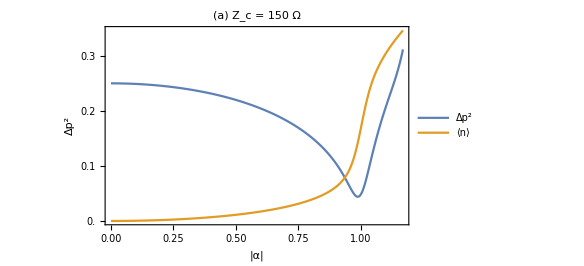

```mathematica
ListPlot[{Transpose[{Range[0.0,1.17,0.005],Chop[dp2ABOCC0]}],
Transpose[{Range[0.0,1.17,0.005],Rescale[#,{0,275}]&/@nAvgABOCC0}]}
,Joined->True
,PlotRange->Full
,Frame->True
,FrameLabel->{{"Δp^2","⟨n⟩"},{"|α|",Automatic}}
,FrameTicks->{{{0.0,0.1,0.2,0.3},{{0,0},{Rescale[25,{0,275}],25},{Rescale[50,{0,275}],50},{Rescale[75,{0,275}],75},{Rescale[100,{0,275}],100}}},{Automatic,Automatic}}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Times New Roman"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Times New Roman"]},{Directive[Black,FontSize->16,FontFamily->"Times New Roman"],Automatic}}
,ImageSize->6 72
,GridLines->{None,{{0.25,Directive[ColorData[97][1],Dashed,Opacity[1]]},{Rescale[pos1,{0,275}],Directive[ColorData[97][2],Dashed,Opacity[1]]}}}
,PlotLegends->Placed[LineLegend[{"Δp^2","⟨n⟩"},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"],LegendFunction->(Framed[#1, FrameMargins-> 0]&)],{0.2,0.25}]
,PlotLabel->Style["(a) Z_c = 150 Ω", Black,16,FontFamily->"Times New Roman"]
]
```

### Solve Z_c=40 Ω

```mathematica
{pos1,aList1}=findMinN[40];
```

```mathematica
pos1
```

159

```mathematica
aTrunc =Floor[600];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
```

```mathematica
Aopc=SparseArray[DiagonalMatrix[(1/aList1[[pos1]])aList1[[;;aTrunc]],1],{aTrunc+1,aTrunc+1}]; 
AopcD=SparseArray[DiagonalMatrix[(1/aList1[[pos1]])aList1[[;;aTrunc]],-1],{aTrunc+1,aTrunc+1}];

AOpc= KroneckerProduct[Aopc,IdentityMatrix[2]];
AOpcD=KroneckerProduct[AopcD,IdentityMatrix[2]];
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
facFunc[n_?IntegerQ]:=Product[AopcDiag[[j]],{j,n}];
```

```mathematica
Product[AopcDiag[[j]],{j,Length[n]}]
```

1

```mathematica
coeff = Table[1.00^k/facFunc[k],{k,350}];
```

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
sop=1/(2 ⅈ)(eop-eop†);
cop=1/2(eop+eop†);
```

### Try a different laser ABOCC operator

```mathematica
stateAnaList = Table[
Module[{coeff,k,normFac},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/AopcDiag[[k]])coeff[[-1]]]
];
normFac=Norm[coeff];
coeff/normFac
]
,{alpha,0.0,1.3,0.005}];
```

```mathematica
dp2ABOCC = Diagonal[stateAnaList*.imOp.imOp.stateAnaListᵀ]-(Diagonal[stateAnaList*.imOp.stateAnaListᵀ])^2;
```

```mathematica
nAvgABOCC=Diagonal[stateAnaList*.aop†.aop.stateAnaListᵀ];
```

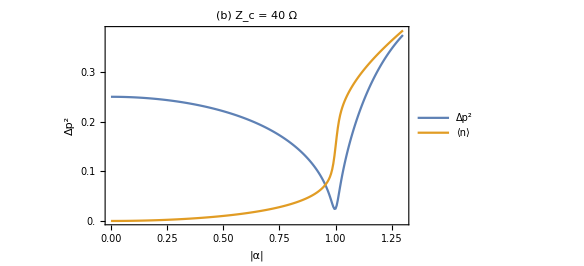

```mathematica
ListPlot[{Transpose[{Range[0.0,1.3,0.005],Chop[dp2ABOCC]}],
Transpose[{Range[0.0,1.3,0.005],Rescale[#,{0,1100}]&/@nAvgABOCC}]}
,Joined->True
,PlotRange->Full
,Frame->True
,FrameLabel->{{"Δp^2","⟨n⟩"},{"|α|",Automatic}}
,FrameTicks->{{{0.0,0.1,0.2,0.3},{{0,0},{Rescale[100,{0,1100}],100},{Rescale[200,{0,1100}],200},{Rescale[300,{0,1100}],300},{Rescale[400,{0,1100}],400}}},{Automatic,Automatic}}
,FrameStyle->{{Directive[ColorData[97][1],FontSize->16,FontFamily->"Times New Roman"],Directive[ColorData[97][2],FontSize->16,FontFamily->"Times New Roman"]},{Directive[Black,FontSize->16,FontFamily->"Times New Roman"],Automatic}}
,ImageSize->6 72
,GridLines->{None,{{0.25,Directive[ColorData[97][1],Dashed,Opacity[1]]},{Rescale[pos1,{0,1100}],Directive[ColorData[97][2],Dashed,Opacity[1]]}}}
,PlotLegends->Placed[LineLegend[{"Δp^2","⟨n⟩"},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"],LegendFunction->(Framed[#1, FrameMargins-> 0]&)],{0.2,0.25}]
,PlotLabel->Style["(b) Z_c = 40 Ω", Black,16,FontFamily->"Times New Roman"]
]
```

## Solve for larger system

### New functions

```mathematica
selectElement[dim_?IntegerQ]:=Module[{center,first,second,third,fourth,fifth},
center =Transpose[{Range[dim],Range[dim]}];
first=Join[ Transpose[{Range[dim-1],Range[2,dim]}],Transpose[{Range[2,dim],Range[dim-1]}]];

second =Join[Transpose[{Range[dim-2],Range[3,dim]}],Transpose[{Range[3,dim],Range[dim-2]}]];

third = Join[Transpose[{Range[dim-3],Range[4,dim]}],Transpose[{Range[4,dim],Range[dim-3]}]];

fourth = Join[Transpose[{Range[dim-4],Range[5,dim]}],Transpose[{Range[5,dim],Range[dim-4]}]];

fifth = Join[Transpose[{Range[1,dim-5,2],Range[6,dim,2]}], Transpose[{Range[6,dim,2],Range[1,dim-5,2]}]];

Return[Join[center,first,second,third,fourth,fifth]]
]
```

```mathematica
makeProj[indexList_,dim_?IntegerQ]:=Module[{},
projRL = ParallelTable[
{(indexList[[k,1]]-1)dim+indexList[[k,2]],k}->1
,{k,Length[indexList]}
];
projector = SparseArray[projRL,{dim*dim,Length[indexList]}];
Return[projector]
]
```

This file is generated by the Main_Manuscript_figures.nb

```mathematica
Get[FileNameJoin[{saveDir,"ABOCC_m0_vs_Zc_data.m"}]];
```

```mathematica
fit=LinearModelFit[{(#[[1]])^-1,#[[2]]}&/@posTb,x,x]
```

FittedModel[0.514286+6356.43 x]

```mathematica
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))]
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.388589

0.156017

```mathematica
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]]
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.996133

0.987903

```mathematica
generateAops[phic_,bigPhi_,rac_,nMax_?IntegerQ,m0_?IntegerQ]:=Module[{Aop1,Aop2},
Quiet[Aop1 = bigPhi Exp[-phic^2/2](1.0 phic aop+Sum[(-1.0)^j phic^(2j+1)/(Factorial[j] Factorial[j+1])MatrixPower[aopᵀ,j].MatrixPower[aop,j+1],{j,1,nMax}])];
Aop2 =2 rac phic aop;

Aopc=Aop1+Aop2;
Aopc=Aopc/(Diagonal[Aopc,1][[m0]]);
]
```

```mathematica
updateABOCCopsNew[zc_?NumericQ]:=Module[{},
m0=Round[fit[1/zc]];
maxN = Round[2.5 m0];


aTrunc =Floor[maxN];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

indexL=selectElement[Length[aOp]];
projector = makeProj[indexL,Length[aOp]];
projectorD=Transpose[projector];

(*aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];*)
sBasis={SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}]],
SparseArray[KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]]};

phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))];
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]];
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];

generateAops[phic,bigPhi,0.418,maxN,m0];
AopcD=Aopcᵀ;

AOpc= KroneckerProduct[Aopc,SparseArray[IdentityMatrix[2]]];
AOpcD=KroneckerProduct[AopcD,SparseArray[IdentityMatrix[2]]];

hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( projectorD.combineOps[hac,iOp].projector-projectorD.combineOps[iOp,hac].projector);
pumpSO = -1/2(projectorD.combineOps[sM.sP,iOp].projector+projectorD.combineOps[iOp,sM.sP].projector-2projectorD.combineOps[sP,sM].projector);
normalLossSO = -1/2(projectorD.combineOps[aOpᵀ.aOp,iOp].projector+projectorD.combineOps[iOp,aOpᵀ.aOp].projector-2 projectorD.combineOps[aOp,aOpᵀ].projector);
lossSO = -1/2(projectorD.combineOps[AOpcᵀ.AOpc,iOp].projector+projectorD.combineOps[iOp,AOpcᵀ.AOpc].projector-2 projectorD.combineOps[AOpc,AOpcᵀ].projector);
Speak["Operators are updated."]
]
```

```mathematica
updateABOCCopsNew[10]
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
resTemppt = Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{12.4535,{-18.9179,{x→3.5,y→1.00204}}}

```mathematica
tempFun2[lambda_?NumericQ,gr_?NumericQ]:=Module[{γ,g},

γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];

steady = SparseArray[Chop[Partition[projector.es[[-1]],Length[aOp]]]];
steady = steady/Tr[steady];

rate = Tr[AOpc.steady.AOpcD];
nAvg = Tr[aOpᵀ.aOp.steady];
Return[{nAvg,rate}]
]
```

```mathematica
resTemp = tempFun2[(x/.resTemppt[[2]]),(y/.resTemppt[[2]])]
```

{699.119-1.17906×10^-8 ⅈ,1.00307-1.64001×10^-12 ⅈ}

### Z_c=100 Ω

```mathematica
{pos1,aList1}=findMinN[50];
```

```mathematica
pos1
```

128

```mathematica
updateABOCCopsNew[100]
```

```mathematica
Dimensions[aop]
```

{161,161}

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
res250 = Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{2.96999,{-12.069,{x→3.61631,y→1.01927}}}

```mathematica
resTemp = tempFun2[(x/.res250[[2]]),(y/.res250[[2]])]
```

{83.5084-2.22722×10^-14 ⅈ,1.03085-2.98256×10^-16 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,161,322}

```mathematica
steady2//Dimensions
```

{322,322}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

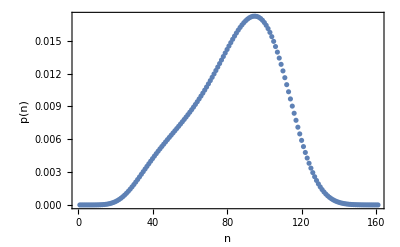

```mathematica
ListPlot[Chop[Diagonal[stateCav2]],Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}]
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00462607,{alpha→1.01464}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

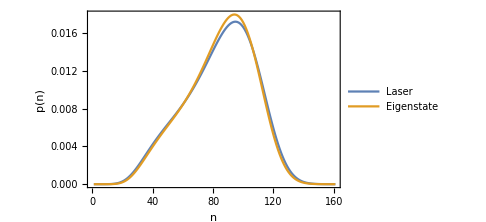

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.2,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.321368,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.312272,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

0

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser, chFun2Dlaser}=generateVectCh4[stateAna,chMeshx,chMeshy,dataDir];
]
]
```

{372.195,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,0,12,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{12221,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{3.58609,Null}

```mathematica
ListContourPlot[wignerD
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/6
,PlotRange->{{4,10},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

-Graphics-

#### Flat top

```mathematica
AbsoluteTiming[
res250v2 = Quiet[FindMinimum[tempfun[x,1.0],{x,3.5,3.4,3.8}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{2.11232,{-11.6561,{x→3.46482}}}

```mathematica
res250
```

{-12.069,{x→3.61631,y→1.01927}}

```mathematica
resTemp = tempFun2[(x/.res250v2[[2]]),1]
```

{67.9047+5.41545×10^-10 ⅈ,1.00058+7.97962×10^-12 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,161,322}

```mathematica
steady2//Dimensions
```

{322,322}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

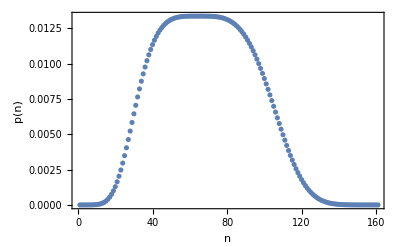

```mathematica
ListPlot[Chop[Diagonal[stateCav2]],Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}]
```

### Z_c=50 Ω

```mathematica
{pos1,aList1}=findMinN[30];
```

```mathematica
pos1
```

212

```mathematica
aTrunc =Floor[500];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
```

```mathematica
Aopc=SparseArray[DiagonalMatrix[1/aList1[[pos1]] aList1[[;;aTrunc]],1],{aTrunc+1,aTrunc+1}]; 
AopcD=SparseArray[DiagonalMatrix[1/aList1[[pos1]] aList1[[;;aTrunc]],-1],{aTrunc+1,aTrunc+1}];

AOpc= KroneckerProduct[Aopc,IdentityMatrix[2]];
AOpcD=KroneckerProduct[AopcD,IdentityMatrix[2]];
```

```mathematica
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( combineOps[hac,iOp]-combineOps[iOp,hac]);
pumpSO = -1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
normalLossSO = -1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
lossSO = -1/2(combineOps[AOpcᵀ.AOpc,iOp]+combineOps[iOp,AOpcᵀ.AOpc]-2 combineOps[AOpc,AOpcᵀ]);
```

```mathematica
iOp=SparseArray[IdentityMatrix[Length[aOp]]];
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
facFunc[n_?IntegerQ]:=Product[AopcDiag[[j]],{j,n}];
```

```mathematica
AopcDiag//Length
```

500

```mathematica
facFunc[2]
```

0.026767

```mathematica
Product[AopcDiag[[j]],{j,Length[n]}]
```

1

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

{ev,es} = Eigensystem[superOp,-3];
steady2 = Partition[Chop[es[[-1]]],Length[aOp]];
steady2 = steady2/Tr[steady2];
Return[Log[Abs[ev[[-2]]]/Abs[Tr[steady2.aOp†.aOp]]^2]]
]
```

```mathematica
res400 = FindMinimum[tempfun[x,y],{x,3.6,3.4,4.0},{y,1.0,0.9,1.1},AccuracyGoal->3,PrecisionGoal->3]
```

{-26.7439,{x→3.85616,y→1.00818}}

```mathematica
res400p = FindMinimum[tempfun[3.67,y],{y,1.0,0.9,1.1},AccuracyGoal->3,PrecisionGoal->3]
```

{-26.7402,{y→1.00869}}

```mathematica
lambdaA=x/.res400[[2]]
gc=lambdaA/2 √(1/(lambdaA - 2 1))
superOp = 1.0 lossSO + lambdaA pumpSO + (y/.res400[[2]])gc HacSO;
```

3.95246

1.41432

```mathematica
superOp = 1.0 lossSO + lambdaA pumpSO + gc HacSO;
```

```mathematica
{eigValR2,eigVectR2}=Eigensystem[superOp,-20];
```

```mathematica
steady2 = Partition[Chop[eigVectR2[[-1]]],Length[aOp]];
steady2 = steady2/Tr[steady2];
```

```mathematica
sBasis//Dimensions
```

{2,401,802}

```mathematica
steady2//Dimensions
```

{802,802}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

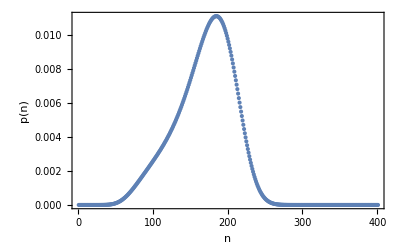

```mathematica
ListPlot[Chop[Diagonal[stateCav2]],Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}]
```

### Z_c = 50 NL

```mathematica
updateABOCCopsNew[50]
```

```mathematica
Dimensions[aop]
```

{321,321}

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
res321= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{8.33657,{-14.1328,{x→3.68084,y→1.00964}}}

```mathematica
resTemp = tempFun2[(x/.res321[[2]]),(y/.res321[[2]])]
```

{156.345-2.14075×10^-14 ⅈ,1.01619-1.6653×10^-16 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,321,642}

```mathematica
steady2//Dimensions
```

{642,642}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00403985,{alpha→1.0076}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

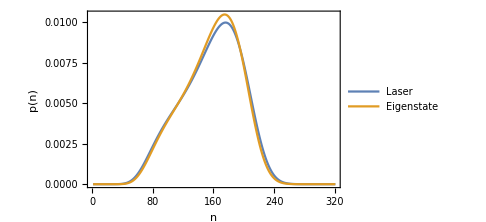

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.2,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{46.9656,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,8,16,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.08013,Null}

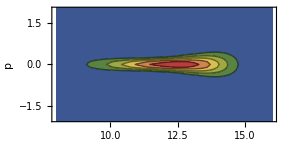

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{8,16},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Z_c = 50 FT

```mathematica
resTemp = tempFun2[(x/.res321[[2]]),1.0]
```

{133.42-3.67987×10^-9 ⅈ,1.00022-7.75085×10^-12 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,321,642}

```mathematica
steady2//Dimensions
```

{642,642}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00322922,{alpha→1.00016}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

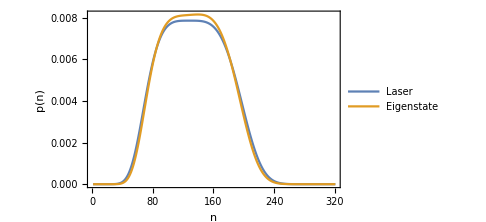

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{52.2556,Null}

```mathematica
Save[FileNameJoin[{saveDir,"FT_ZC_50_Character_function.m"}],{chMesh2Dlaser3, chFun2Dlaser3}]
```

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,7,15,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.7089,Null}

```mathematica
Speak["This is done"]
```

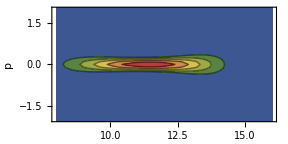

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{8,16},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Z_c = 100 NL

```mathematica
updateABOCCopsNew[100]
```

```mathematica
Dimensions[aop]
```

{161,161}

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
res250= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{3.17289,{-12.069,{x→3.61631,y→1.01927}}}

```mathematica
resTemp = tempFun2[(x/.res250[[2]]),(y/.res250[[2]])]
```

{83.5084-2.22722×10^-14 ⅈ,1.03085-2.98256×10^-16 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,161,322}

```mathematica
steady2//Dimensions
```

{322,322}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00462607,{alpha→1.01464}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.2,0.8}]]
```

-Graphics-

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{33.7177,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,5,13,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.07713,Null}

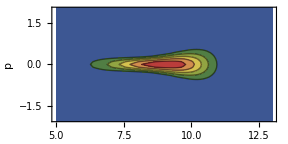

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{5,13},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Z_c = 100 FT

```mathematica
resTemp = tempFun2[(x/.res250[[2]]),1.0]
```

{67.9968+1.98506×10^-15 ⅈ,1.00062+1.97928×10^-17 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,161,322}

```mathematica
steady2//Dimensions
```

{322,322}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00363843,{alpha→1.00036}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

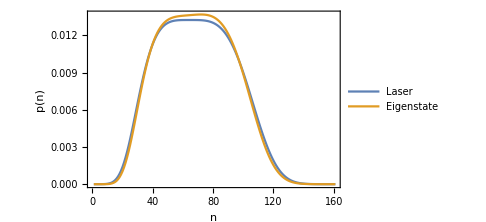

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{37.1197,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,4,12,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.05761,Null}

```mathematica
Speak["This is done"]
```

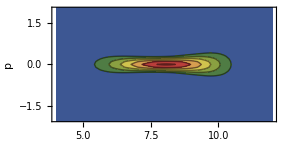

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{4,12},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Z_c =40 NL

```mathematica
updateABOCCopsNew[40]
```

```mathematica
Dimensions[aop]
```

{399,399}

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
res400= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{7.26211,{-14.7943,{x→3.66962,y→1.00772}}}

```mathematica
resTemp = tempFun2[(x/.res400[[2]]),(y/.res400[[2]])]
```

{191.513+9.31601×10^-10 ⅈ,1.0129+2.13344×10^-12 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00361456,{alpha→1.00606}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

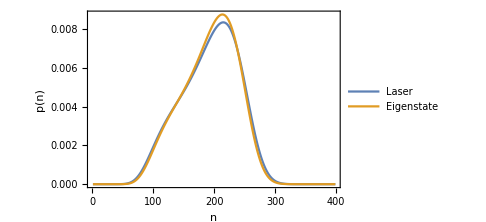

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.2,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{70.9416,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,9,17,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.14704,Null}

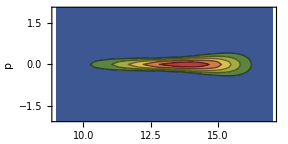

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{9,17},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Z_c = 40 FT

```mathematica
resTemp = tempFun2[(x/.res400[[2]]),1.0]
```

{165.919+3.05511×10^-9 ⅈ,1.00016+4.09082×10^-12 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,399,798}

```mathematica
steady2//Dimensions
```

{798,798}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00292974,{alpha→1.00012}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

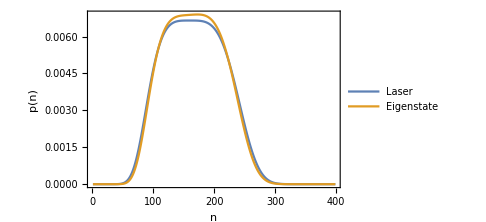

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{68.6948,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,9,17,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.06746,Null}

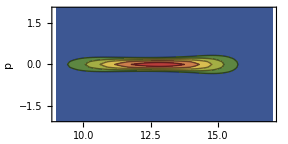

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{9,17},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

### Z_c = 30 NL

```mathematica
updateABOCCopsNew[30]
```

```mathematica
Dimensions[aop]
```

{531,531}

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
res530= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{22.1156,{-15.6484,{x→3.65936,y→1.00579}}}

```mathematica
resTemp = tempFun2[(x/.res530[[2]]),(y/.res530[[2]])]
```

{249.453+3.74743×10^-9 ⅈ,1.00963+1.4685×10^-12 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,531,1062}

```mathematica
steady2//Dimensions
```

{1062,1062}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00314741,{alpha→1.00452}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

```mathematica
stateAna3=stateAna3[[;;401]];
```

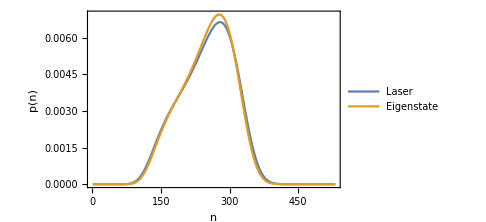

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.2,0.8}]]
```

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.326277,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.31106,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{33.7177,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,5,13,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.07713,Null}

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{5,13},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

-Graphics-

### Z_c = 100 FT

```mathematica
resTemp = tempFun2[(x/.res250[[2]]),1.0]
```

{67.9968+1.98506×10^-15 ⅈ,1.00062+1.97928×10^-17 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,161,322}

```mathematica
steady2//Dimensions
```

{322,322}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00363843,{alpha→1.00036}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.8,0.8}]]
```

-Graphics-

#### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.319837,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.321238,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

0

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{709.565,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,4,12,0.1},{y,-5,5,0.1}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{8181,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.54196,Null}

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
(*,PlotRange->Full*)
,AspectRatio->4/8
,PlotRange->{{4,12},{-2,2},All}
,ImageSize->4 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Top]
]
```

-Graphics-

## Sweep the ΔS phase noise

```mathematica
testFun[ratio_?NumericQ,AopcDiag_,stateCav2_]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];

stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha,AopcDiag,stateCav2],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00322875,{alpha→1.00062}}

```mathematica
narrowAlpha=FindMinimum[testFun[alpha,AopcDiag,stateCav2],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00462607,{alpha→1.01464}}

```mathematica
resTemp= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
```

{-21.7434,{x→3.49999,y→1.0001}}

```mathematica
Monitor[
allNoiseTable=Table[
updateABOCCopsNew[1/value];
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
resTemp= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]];
AopcDiag=Diagonal[Aopc,1];
tempFun2[(x/.resTemp[[2]]),(y/.resTemp[[2]])];
steady2 = steady;
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;narrowAlpha=Quiet[FindMinimum[testFun[alpha,AopcDiag,stateCav2],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]];
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
normFac = Norm[coeff]; 
stateAna3 = coeff/normFac; 

tempFun2[(x/.resTemp[[2]]),1];
steady2 = steady;
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
narrowAlpha=Quiet[FindMinimum[testFun[alpha,AopcDiag,stateCav2],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]];
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
normFac = Norm[coeff]; 
stateAna4 = coeff/normFac; 

sop=1/(2 ⅈ)(eop-eop†);
cop=1/2(eop+eop†);

(*NL ABOCC eigen*)
nlRes = {
stateAna3*.aop†.aop.stateAna3,
stateAna3*.reOp.reOp.stateAna3-(stateAna3*.reOp.stateAna3)^2,
stateAna3*.imOp.imOp.stateAna3-(stateAna3*.imOp.stateAna3)^2,
√(stateAna3*.reOp.reOp.stateAna3-(stateAna3*.reOp.stateAna3)^2)√(stateAna3*.imOp.imOp.stateAna3-(stateAna3*.imOp.stateAna3)^2),
stateAna3*.aop†.aop.aop†.aop.stateAna3-(stateAna3*.aop†.aop.stateAna3)^2,
√(stateAna3*.sop.sop.stateAna3-(stateAna3*.sop.stateAna3)^2),
stateAna3*.sop.sop.stateAna3-(stateAna3*.sop.stateAna3)^2,
√(stateAna3*.aop†.aop.aop†.aop.stateAna3-(stateAna3*.aop†.aop.stateAna3)^2)√(stateAna3*.sop.sop.stateAna3-(stateAna3*.sop.stateAna3)^2),
(stateAna3*.aop†.aop.aop†.aop.stateAna3-(stateAna3*.aop†.aop.stateAna3)^2)(stateAna3*.sop.sop.stateAna3-(stateAna3*.sop.stateAna3)^2)/((stateAna3*.cop.stateAna3)^2),
(stateAna3*.sop.sop.stateAna3-(stateAna3*.sop.stateAna3)^2)/((stateAna3*.cop.stateAna3)^2)
};

(*Flat top ABOCC eigen*)
ftRes = {
stateAna4*.aop†.aop.stateAna4,
stateAna4*.reOp.reOp.stateAna4-(stateAna4*.reOp.stateAna4)^2,
stateAna4*.imOp.imOp.stateAna4-(stateAna4*.imOp.stateAna4)^2,
√(stateAna4*.reOp.reOp.stateAna4-(stateAna4*.reOp.stateAna4)^2)√(stateAna4*.imOp.imOp.stateAna4-(stateAna4*.imOp.stateAna4)^2),
stateAna4*.aop†.aop.aop†.aop.stateAna4-(stateAna4*.aop†.aop.stateAna4)^2,
√(stateAna4*.sop.sop.stateAna4-(stateAna4*.sop.stateAna4)^2),
stateAna4*.sop.sop.stateAna4-(stateAna4*.sop.stateAna4)^2,
√(stateAna4*.aop†.aop.aop†.aop.stateAna4-(stateAna4*.aop†.aop.stateAna4)^2)√(stateAna4*.sop.sop.stateAna4-(stateAna4*.sop.stateAna4)^2),
(stateAna4*.aop†.aop.aop†.aop.stateAna4-(stateAna4*.aop†.aop.stateAna4)^2)(stateAna4*.sop.sop.stateAna4-(stateAna4*.sop.stateAna4)^2)/((stateAna4*.cop.stateAna4)^2),
(stateAna4*.sop.sop.stateAna4-(stateAna4*.sop.stateAna4)^2)/((stateAna4*.cop.stateAna4)^2)
};
{1/value,nlRes,ftRes}
,{value,1/150.0,1/10.0,(0.1-1/150.)/31}];
,1/value]
```

```mathematica
NSolve[fit[x]==600,x]
```

{{x→0.0943117}}

```mathematica
m0List ={(x/. NSolve[fit[x]==#,x][[1]]),#}&/@Range[100,600,100]
```

{{0.0156512,100},{0.0313833,200},{0.0471154,300},{0.0628475,400},{0.0785796,500},{0.0943117,600}}

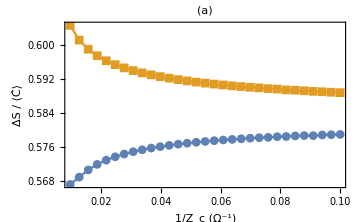

```mathematica
ListPlot[{{1/#[[1]],(#[[2,9]])^(1/2)}&/@allNoiseTable[[2;;]],{1/#[[1]],(#[[3,9]])^(1/2)}&/@allNoiseTable[[2;;]]}
,PlotRange->Full
,Joined->True
,PlotMarkers->Automatic
,ImageSize->5 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{{"ΔS / ⟨Ĉ⟩ ",None},{"1/Z_c (Ω^-1)","m_0"}}
(*,FrameLabel->{"1/Z_c (Ω^-1)","ΔS / ⟨c⟩"}*)
,FrameTicks->{{Automatic,Automatic},{Automatic,m0List}}
,ImageSize->5 72
,PlotLabel->Style["(a)",Black,16,FontFamily->"Times New Roman"]
]
```

```mathematica
aTrunc =Floor[900];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
sop=1/(2 ⅈ)(eop-eop†);
cop=1/2(eop+eop†);
```

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
cohStateNSNoise  =Table[

cohState =Chop[ coh[√allNoiseTable[[j,2,1]],900]];

res = {
cohState*.aop†.aop.cohState,
cohState*.reOp.reOp.cohState-(cohState*.reOp.cohState)^2,
cohState*.imOp.imOp.cohState-(cohState*.imOp.cohState)^2,
√(cohState*.reOp.reOp.cohState-(cohState*.reOp.cohState)^2)√(cohState*.imOp.imOp.cohState-(cohState*.imOp.cohState)^2),
cohState*.aop†.aop.aop†.aop.cohState-(cohState*.aop†.aop.cohState)^2,
√(cohState*.sop.sop.cohState-(cohState*.sop.cohState)^2),
cohState*.sop.sop.cohState-(cohState*.sop.cohState)^2,
√(cohState*.aop†.aop.aop†.aop.cohState-(cohState*.aop†.aop.cohState)^2)√(cohState*.sop.sop.cohState-(cohState*.sop.cohState)^2),
(cohState*.aop†.aop.aop†.aop.cohState-(cohState*.aop†.aop.cohState)^2)(cohState*.sop.sop.cohState-(cohState*.sop.cohState)^2)/((cohState*.cop.cohState)^2),
(cohState*.sop.sop.cohState-(cohState*.sop.cohState)^2)/((cohState*.cop.cohState)^2)
};
res
,{j,2,Length[allNoiseTable]}];
```

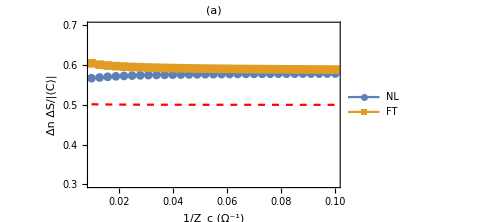

```mathematica
p1=Show[
ListPlot[{{1/#[[1]],(#[[2,9]])^(1/2)}&/@allNoiseTable[[2;;]],{1/#[[1]],(#[[3,9]])^(1/2)}&/@allNoiseTable[[2;;]]}
,PlotRange->{{0.01,0.1},{0.3,0.7}}
,Joined->True
,PlotMarkers->Automatic
,ImageSize->5 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{{"Δn ΔS/|⟨C⟩|",None},{"1/Z_c (Ω^-1)","m_0"}}
(*,FrameLabel->{"1/Z_c (Ω^-1)","ΔS / ⟨c⟩"}*)
,FrameTicks->{{Automatic,Automatic},{Automatic,m0List}}
,ImageSize->5 72
,PlotLabel->Style["(a)",Black,16,FontFamily->"Times New Roman"]
,PlotLegends->Placed[LineLegend[{"NL","FT"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],LegendFunction->(Framed[#1,FrameMargins-> 0.1,FrameStyle->Thickness[0.1]] & )],{0.2,0.25}]
]
,ListLinePlot[Transpose[{allNoiseTable[[2;;,1]]^-1,cohStateNSNoise[[All,9]]^(1/2)}],
PlotStyle->{Red,Dashed}]
]
```

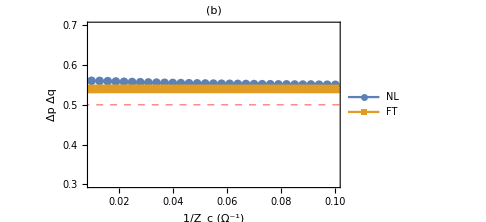

```mathematica
p2=ListPlot[{{1/#[[1]],(#[[2,4]])^(1/2)}&/@allNoiseTable[[2;;]],{1/#[[1]],(#[[3,4]])^(1/2)}&/@allNoiseTable[[2;;]]}
,PlotRange->{{0.01,0.1},{0.3,0.7}}
,Joined->True
,PlotMarkers->Automatic
,ImageSize->5 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{{"Δp Δq",None},{"1/Z_c (Ω^-1)","m_0"}}
(*,FrameLabel->{"1/Z_c (Ω^-1)","ΔS / ⟨c⟩"}*)
,FrameTicks->{{Automatic,Automatic},{Automatic,m0List}}
,ImageSize->5 72
,PlotLabel->Style["(b)",Black,16,FontFamily->"Times New Roman"]
,GridLines->{None,{{0.5,Directive[Red,Dashed,Opacity[1],Thick]}}}
,PlotLegends->Placed[LineLegend[{"NL","FT"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],LegendFunction->(Framed[#1,FrameMargins-> 0.1,FrameStyle->Thickness[0.1]] & )],{0.2,0.25}]
]
```

```mathematica
ft = LinearModelFit[{Log[fit[1/#[[1]]]],Log[(#[[2,5]])^(1/2)]}&/@allNoiseTable[[2;;]],x,x]
```

FittedModel[-0.0514972+0.761495 x]

```mathematica
zcList={fit[1/#],#}&/@{100,75,50,40,30,20,10}
```

{{64.0786,100},{85.2667,75},{127.643,50},{159.425,40},{212.395,30},{318.336,20},{636.157,10}}

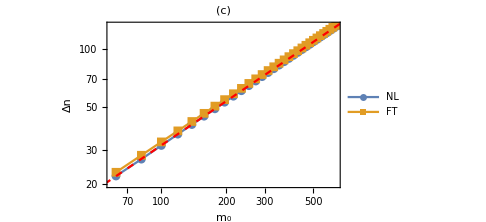

```mathematica
p3=Show[
ListLogLogPlot[{{fit[1/#[[1]]],(#[[2,5]])^(1/2)}&/@allNoiseTable[[2;;]],{fit[1/#[[1]]],(#[[3,5]])^(1/2)}&/@allNoiseTable[[2;;]]}
,PlotRange->Full
,Joined->True
,PlotMarkers->Automatic
,ImageSize->5 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{{"Δn",None},{"m_0","Z_c (Ω)"}}
(*,FrameLabel->{"1/Z_c (Ω^-1)","ΔS / ⟨c⟩"}*)
,FrameTicks->{{Automatic,Automatic},{{100,200,300,400,500},zcList}}
,ImageSize->5 72
,PlotLabel->Style["(c)",Black,16,FontFamily->"Times New Roman"]
(*,GridLines->{None,{{0.5,Directive[Red,Dashed,Opacity[1],Thick]}}}*)
,PlotLegends->Placed[LineLegend[{"NL","FT"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],LegendFunction->(Framed[#1,FrameMargins-> 0.1,FrameStyle->Thickness[0.1]] & )],{0.75,0.25}]
]
,Plot[ft[x],{x,-100,100},PlotRange->Full,PlotStyle->Directive[Red,Dashed]]
]
```

## Shfit phase phase

### Z_c = 50 NL

```mathematica
updateABOCCopsNew[100]
```

```mathematica
Dimensions[aop]
```

{161,161}

```mathematica
reOp=1/2(aop+aop†);
imOp=1/(2ⅈ)(aop-aop†);
```

```mathematica
tempfun[lambda_?NumericQ,gr_?NumericQ]:=Module[{g,γ},
γ=1.0;
g=gr lambda/2 √(γ/(lambda - 2 γ));
superOp = lambda pumpSO + γ lossSO +  g HacSO;

ev = Eigenvalues[superOp,-3];
Return[Log[Abs[ev[[-2]]]]]
]
```

```mathematica
AbsoluteTiming[
resTemppt= Quiet[FindMinimum[tempfun[x,y],{x,3.5,3.4,3.8},{y,1.0,0.95,1.05}(*,PrecisionGoal->5,AccuracyGoal->5*)]]
]
```

{2.90825,{-12.069,{x→3.61631,y→1.01927}}}

```mathematica
resTemp = tempFun2[(x/.resTemppt[[2]]),(y/.resTemppt[[2]])]
```

{83.5084-2.22722×10^-14 ⅈ,1.03085-2.98256×10^-16 ⅈ}

```mathematica
steady2 = steady;
```

```mathematica
sBasis//Dimensions
```

{2,161,322}

```mathematica
steady2//Dimensions
```

{322,322}

```mathematica
stateCav2= sBasis[[1]].steady2.sBasis[[1]]†+sBasis[[2]].steady2.sBasis[[2]]†;
```

```mathematica
AopcDiag=Diagonal[Aopc,1];
```

```mathematica
testFun[ratio_?NumericQ]:=Module[{stateTemp,coeff,diff},
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,ratio/AopcDiag[[k]] coeff[[-1]]]
];
stateTemp = coeff/Norm[coeff];
diff = Total[Abs[stateTemp^2-Diagonal[stateCav2]]^2];
Return[diff^(1/2)]]
```

```mathematica
narrowAlpha=FindMinimum[testFun[alpha],{alpha,1,0.9,1.4},PrecisionGoal->4,AccuracyGoal->4]
```

{0.00462607,{alpha→1.01464}}

```mathematica
coeff={1};
For[k=1,k≤Length[aop]-1,k+=1,
AppendTo[coeff,(alpha/.narrowAlpha[[2]])/AopcDiag[[k]] coeff[[-1]]]
];
```

```mathematica
normFac = Norm[coeff];
```

```mathematica
stateAna3 = coeff/normFac;
```

```mathematica
ListPlot[{Chop[Diagonal[stateCav2]],Abs[stateAna3]^2},Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"n","p(n)"}
,Joined->True
,ImageSize->5 72
,PlotLegends->Placed[LineLegend[{"Laser","Eigenstate"},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]],{0.2,0.8}]]
```

-Graphics-

```mathematica
stateAna3 = Exp[ⅈ π/4 Range[0,Length[stateAna3]-1]] stateAna3;
```

### Calculate the above Wigner function

```mathematica
chMeshx=Range[-2.,2.,0.1];
chMeshy=Range[-6.,6.,0.1];
```

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.316349,{}}

```mathematica
AbsoluteTiming[
notExist = checkChMesh2[chMeshx,chMeshy,dataDir]
]
```

{0.306386,{}}

```mathematica
notExist = checkChMesh2[chMeshx,chMeshy,dataDir];
Length[notExist]
While[Length[notExist]≠0,
generateMissingPts[notExist,dataDir];
notExist= checkChMesh2[chMeshx,chMeshy,dataDir];
]
```

0

```mathematica
AbsoluteTiming[
If[Length[notExist]==0,
{chMesh2Dlaser3, chFun2Dlaser3}=generateVectCh4[stateAna3,chMeshx,chMeshy,dataDir];
]
]
```

{105.366,Null}

```mathematica
chMeshxEx=Join[Range[-10.,-2.1,0.1],Range[2.1,10,0.1]];
chMeshyEx=Join[Range[-10.,-6.1,0.1],Range[6.1,10,0.1]];
```

```mathematica
chMeshExMesh=Transpose[{Flatten[ConstantArray[chMeshxEx,Length[chMeshyEx]]],Flatten[Transpose[ConstantArray[chMeshyEx,Length[chMeshxEx]]]]}];
```

```mathematica
chFun2DlaserEx=ConstantArray[0,Length[chMeshExMesh]];
```

```mathematica
wigMesh=Table[
{x,y}
,{x,4,9,0.05},{y,4,9,0.05}];
wigMesh=Flatten[wigMesh,1];
Dimensions[wigMesh]
```

{10201,2}

```mathematica
chFun2DlaserAll=SparseArray[Join[chFun2Dlaser3,chFun2DlaserEx]];
chMesh2DlaserAll=Join[chMesh2Dlaser3,chMeshExMesh];
```

```mathematica
AbsoluteTiming[
wignerD3 = solveWD[chFun2DlaserAll,chMesh2DlaserAll,wigMesh];
]
```

{2.30702,Null}

```mathematica
ListContourPlot[wignerD3
(*,PlotRange->Full*)
,ColorFunction->"DarkRainbow"
,Contours->Range[0.1,0.6,0.1]
,PlotRange->Full
(*,AspectRatio->4/8*)
(*,PlotRange->{{8,16},{-2,2},All}*)
,ImageSize->5 72
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"]
,FrameLabel->{"q","p"}
,PlotLegends->Placed[
BarLegend[Automatic,LegendLabel->"W(q,p)",LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"]]
,Right]
]
```

-Graphics-